# Ising modelled using the Metropolis algorithm

## Definition of the lattice

{,}

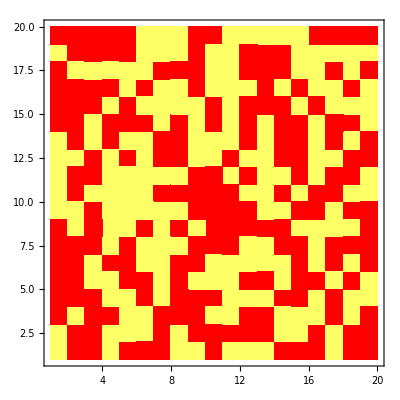

```mathematica
{Slider[Dynamic[size],{1,50,1}],Dynamic[size]} 
Clear[s];
s=Table[If[Random[Integer]==0,1,-1],{i,1,size},{j,1,size}];
plotit:=ListDensityPlot[s,Mesh->False,InterpolationOrder->0,PlotRange->{-1,1},ColorFunction->(RGBColor[3,#,0.4#]&)];
plotit
```

## Compute the change in energy

```mathematica
deltaU[i_,j_]:=2*s[[i,j]]*(
If[i==1,s[[size,j]],s[[i-1,j]]]
+If[i==size,s[[1,j]],s[[i+1,j]]]
+If[j==1,s[[i,size]],s[[i,j-1]]]
+If[j==size,s[[i,1]],s[[i,j+1]]])
```

## Execute the Metropolis algorithm

```mathematica
runawhile[T_,stepcount_]:=(
For[step=0,step<stepcount,step++,i=RandomInteger[{1,size}];
j=RandomInteger[{1,size}];
Ediff=deltaU[i,j];
If[Ediff≤0,s[[i,j]]=-s[[i,j]],If[RandomReal[]<Exp[-Ediff/T],s[[i,j]]=-s[[i,j]]]]];
plotit)
```

## Static model

```mathematica
(*runawhile[2.27,100*size^2]*)
```

## Animated model

```mathematica
ListAnimate[Table[runawhile[2.27,size^2],{plotnum,1,20}]]
```